# Time-independent scattering theory

## Notes

Nirav Mehta (2019)

Trinity University, San Antonio

## Introduction

These notes will hopefully provide an introduction to the time independent theory of scattering that is accessible to undergraduate and beginning graduate students who wish to begin research in this area.  Many textbooks on the topic already exist, but these notes are my attempt to provide a succinct treatment designed to get students started quickly.

## Multichannel 2-body Scattering

### Basic expression for the differential cross section

I’ll focus on scattering in two-body channels only.  Other processes like three-body recombination, break-up, or any process involving channels with more than two free particles will be treated elsewhere.  I’ll assume that each collision partner has some set of internal states.  The collective variables for the internal degrees of freedom for both collision partners will be ξ.  The full (relative) wavefunction can then be expanded:

Ψ(r,ξ)=∑_i ψ_i(r)Υ_i(ξ)

Υ_i(ξ) denotes the orthonormal set of wavefunctions in all internal coordinates ξ. We’ll assume that they are known to satisfy:

H_ξ Υ_i(ξ)=E_i Υ_i(ξ)

Here we assume that H_ξ is independent of r.  It is the Hamiltonian of the well-separated collision partners. The full wavefunction satisfies

(-ℏ^2/(2μ)∇^2 +H_ξ+W(r,ξ))Ψ(r,ξ)=E Ψ(r,ξ)

We assume W(r,ξ)→0 as r→∞.  Asymptotically, the wavefunction should take the form

Ψ(r,ξ)→^(r→ ∞)Υ_i(ξ)ⅇ^(ⅈ k_i z)+∑_(j∈open) f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r Υ_j(ξ)

The first term represents the incident wave in internal state i (remember i is a collective index for the internal state of both particles), which we assume to be travelling in the z direction.  The second term represents the scattered wave which moves radially away from the collision in channel j with an overall amplitude that depends on θ and ϕ.  Here, k_i^2=2μ (E-E_i)/ℏ^2.  We can interpret the coordinates ξ and r in terms of Jacobi coordinates if we picture “H-type” Jacobi coordinates for the global few-body system.  I’m sweeping details like the exchange interaction (important at short range) under the rug here by absorbing those effects into the interaction potential W(r,ξ).

Consider the overlap of the asymptotic wavefunction with Υ_j(ξ),

ψ_j(r)=∫ⅆξ Υ_j(ξ)Ψ(r,ξ)→^(r→∞)(δ_ji ⅇ^(ⅈ k_i z))^(⏞^(incoming in 
channel i only))+(f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r)^(⏞^(outgoing in channel j))

Recall that the probability current density is given by j=ℏ/(2μ ⅈ)(ψ*∇ψ-ψ∇ψ*).  The incoming flux is .

j_in=δ_ji(ℏ ẑ)/(2μ ⅈ)(ⅇ^(-ⅈ k_i z)(ⅈ k_i)ⅇ^(ⅈ k_i z)-ⅇ^(ⅈ k_i z)(-ⅈ k_i)ⅇ^(-ⅈ k_i z))=δ_ji(ℏ k_i)/μ ẑ

Meanwhile, the total outgoing flux is:

j_out=∑_(j∈open) (ℏ r̂)/(2μ ⅈ)((|f|)^2 ⅇ^(-ⅈ k_j r)/r(ⅈ k_j ⅇ^(ⅈ k_j r)/r-ⅇ^(ⅈ k_j r)/r^2)-(|f|)^2 ⅇ^(ⅈ k_j r)/r(-ⅈ k_j ⅇ^(-ⅈ k_j r)/r-ⅇ^(-ⅈ k_j r)/r^2))

j_out=∑_(j∈open) (ℏ k_j)/(μ r^2)(|f_(i→j)|)^2 r̂

The flux going into a surface ⅆσ ẑ must exit a surface r^2 ⅆΩ r̂ so we have:

j_in·ⅆσ ẑ=j_out·r^2ⅆΩ r̂

(δ_ji(ℏ k_i)/μ ẑ)·ⅆσ ẑ=(∑_(j∈open) (ℏ k_j)/(μ r^2)(|f_(i→j)|)^2 r̂)·r^2ⅆΩ r̂

ⅆσ/ⅆΩ=∑_(j∈open) k_j/k_i(|f_(i→j)|)^2

We define:

(ⅆσ/ⅆΩ)_(i→j)=k_j/k_i(|f_(i→j)|)^2

We shall expend considerable effort determining f_(i→j).

### Coupled-channel equations and the partial wave expansion

Now inserting our expansion into the Schrodinger equation,

(-ℏ^2/(2μ)∇^2 +H_ξ+W(r,ξ))∑_i ψ_i(r)Υ_i(ξ)=E ∑_i ψ_i(r)Υ_i(ξ)

Using the eigenvalue relation H_ξ Υ_i(ξ)=E_i Υ_i(ξ) we have

∑_i (-ℏ^2/(2μ)∇^2 +E_i+W(r,ξ))ψ_i(r)Υ_i(ξ)=E ∑_i ψ_i(r)Υ_i(ξ).

Now taking the overlap with Υ_j(ξ) gives us a coupled-channels equation:

(-ℏ^2/(2μ)∇^2)ψ_j(r)+∑_i W_ji(r)ψ_i(r)=(E-E_j) δ_ji ψ_j(r),

where we have used ∫ⅆξΥ_j(ξ)Υ_i(ξ)=δ_ji and defined

W_ji(r)=∫ⅆξΥ_j(ξ)W(r,ξ)Υ_i(ξ).

We now expand each channel wavefunction into partial waves:

ψ_i(r)=(∑_(l=0))^∞(∑_(m=-l))^l(u_(i l m)(r))/r Y_(l m)(θ,ϕ)

Note that -ℏ^2/(2μ)∇^2 =-ℏ^2/(2μ) 1/r^2∂/(∂r)(r^2∂/(∂r))+L^2/(2μ r^2) where L^2 is the (square) orbital angular momentum operator L^2 Y_(l m)(θ,ϕ)=ℏ^2 l(l+1)Y_(l m)(θ,ϕ).  Also, 1/r^2∂/(∂r)(r^2∂/(∂r)(u_(i l m)(r))/r)=1/r∂^2/(∂r^2)u_(i l m)(r).  Therefore, our coupled channels equation becomes:

∑_(l,m) (-ℏ^2/(2μ) 1/r^2∂/(∂r)(r^2∂/(∂r))+L^2/(2μ r^2))(u_(j l m)(r))/r Y_(l m)(θ,ϕ)+∑_(i,l,m) W_ji(r)(u_(i l m)(r))/r Y_(l m)(θ,ϕ)=(E-E_j) δ_ji(u_(j l m)(r))/r Y_(l m)(θ,ϕ)

∑_(l,m) 1/r(-ℏ^2/(2μ) (∂^2 u_(j l m)(r))/(∂r^2)+(ℏ^2 l(l+1)u_(j l m)(r))/(2μ r^2))Y_(l m)(θ,ϕ)+∑_(i,l,m) W_ji(r)(u_(i l m)(r))/r Y_(l m)(θ,ϕ)=(E-E_j) δ_ji∑_(l,m) (u_(j l m)(r))/r Y_(l m)(θ,ϕ)

Now we take the overlap with Y_(l' m')(θ,ϕ) to find (after trivial re-labeling):

(-ℏ^2/(2μ) (∂^2 u_(i l m)(r))/(∂r^2)+(ℏ^2 l(l+1)u_(i l m)(r))/(2μ r^2))+∑_(j,l',m') V_(i l m, j l'm')(r)u_(j l' m')(r)=(E-E_i) u_(i l m)(r)

Where we have defined

V_(i l m, j l'm')(r)=∫ⅆξⅆΩ Υ_i(ξ)Y_(l m)(θ,ϕ)W(r,ξ)Υ_j(ξ)Y_(l' m')(θ,ϕ)=∫ⅆΩY_(l m)(θ,ϕ)W_ij(r)Y_(l' m')(θ,ϕ).

If W_ij(r) is spherically symmetric, then V_(i l m, j l'm')(r)=δ_(l,l')δ_(m,m')V_ij(r) and each partial wave (l,m) can be treated separately. This is not the case, for example, when we have a collision between polar molecules or atoms with strong magnetic moments.

### Asymptotic solutions to the coupled equations

We assume that sufficiently far away from the collision center, the potential matrix elements all vanish

V_(i l m, j l'm')(r)→^(r→∞)0

and so we seek solutions to

(-(∂^2 u_(i l m)(r))/(∂r^2)+(l(l+1)u_(i l m)(r))/r^2)=k_i^2 u_(i l m)(r)

(-∂^2/(∂(k_i r)^2)+(l(l+1))/(k_i r)^2-1)u_(i l m)(r)=0

The solutions are the Riccati-Bessel functions

u_(i l m)(r)→ Piecewise[{{s_l(k_i r)=k_i rj_l(k r)→^(k_i r ≫1)sin(k_i r-l π/2), }, {c_l(k_i r)=-k_irn_l(k r)→^(k_i r ≫1)cos(k_i r-l π/2), }}]

Here, j_l(x) and n_l(x) are the spherical Bessel and Neumann functions, respectively.  One could equivalently use Hankel-type functions:

u_(i l m)(r)→ Piecewise[{{f^(+)(k_i r)= (c_l+ⅈ s_l)=ⅈ k_i rh_l^(1)(k_i r)=ⅈ k_i r (j_l+ⅈ n_l)→^(k_i r ≫1)(-ⅈ)^l ⅇ^(ⅈ k_i r), }, {f^(-)(k_i r)=(c_l-ⅈ s_l)=-ⅈ k_i r h_l^(2)(k_i r)=-ⅈ k_i r (j_l-ⅈ n_l)→^(k_i r ≫1)ⅈ^l ⅇ^(-ⅈ k_i r), }}]

In some cases, we’ll need the solutions for closed channels.  In this case, k_i^2→-κ_i^2=2μ (E-E_i)/ℏ^2<0.  Asymptotically we have

(∂^2/(∂(κ_i r)^2)-(l(l+1))/(κ_i r)^2-1)u_(i l m)(r)=0

u_(i l m)(r)→ Piecewise[{{2/π κ_i r k_l(κ_i r)=√(2/π κ_i r)K_(l+1/2)(κ_i r)→^(k_i r ≫1)√(2/π κ_i r)√(π/(2 κ_i r))ⅇ^-κ_ir=ⅇ^-κ_ir, }, {2/π κ_i r i_l(κ_i r)=√(2/π κ_i r)I_(l+1/2)(κ_i r)→^(k_i r ≫1)√(2/π κ_i r)ⅇ^(κ_i r)/(√(2π κ_i r))=ⅇ^(κ_i r)/π, }}]

### Orthogonality of the j_l,n_l functions

The scattering solutions s_l(k r) and c_l(k r) are oscillatory at large r and never decay to zero.  They cannot be normalized in the usual way that one may normalize bound-state wavefunctions ∫ⅆr (|ψ|)^2=1.  Note, however, that

∫_0^∞ ⅆr r^2 j_l(k_i r)j_l(k_j r)=π/2(δ(k_i-k_j))/k_i^2

How can we prove this relation?  I’ll start with the Fourier theorem:

f(r)=∫ⅆk/(2π)^3 ⅇ^(ⅈ k·r)F(k)

where the Fourier transform of f(r) is given by

F(k)=∫ⅆr ⅇ^(-ⅈ k·r)f(r)

Insert the first expression into the second, but use a dummy variable q for the integration:

F(k)=∫ⅆr ⅇ^(-ⅈ k·r)∫ⅆq/(2π)^3 ⅇ^(ⅈ q·r)F(q)

F(k)=∫ⅆq/(2π)^3(∫ⅆr ⅇ^(-ⅈ k·r)ⅇ^(ⅈ q·r))F(q)

F(k)=∫ⅆq/(2π)^3(∫ⅆr ⅇ^(-ⅈ (k-q)·r))F(q)

This can only be true if

∫ⅆr ⅇ^(-ⅈ (k-q)·r)=(2π)^3 δ^3(k-q)

Now the plane wave can be expanded as (I’m not going to prove this):

ⅇ^(ⅈ k·r)=4π(∑_(l=0))^∞ⅈ^l j_l(k r)(∑_(m=-l))^l(Y*)_(l,m)(k̂)Y_(l,m)(r̂)

Let’s take a look at:

∫ⅆr ⅇ^(-ⅈ (k-q)·r)=(∑_(l=0))^∞(∑_(m=-l))^l(∑_(l'=0))^∞(∑_(m'=-l'))^l'(ⅈ^(l+l')(4π))^2(Y*)_(l,m)(k̂)Y_(l',m')(q̂)∫ⅆr r^2  j_l(k r)j_l'(q r)(∫ⅆΩ Y_(l,m)(r̂) (Y*)_(l',m')(r̂))^(⏞^(δ_(l,l')δ_(m,m')))

∫ⅆr ⅇ^(-ⅈ (k-q)·r)=(∑_(l=0))^∞(∑_(m=-l))^l ⅈ^(2l) (4π)^2(Y*)_(l,m)(k̂)(Y*)_(l,m)(q̂)∫ⅆr r^2  j_l(k r)j_l(q r)

For integer l, ⅈ^(2l)=1 and the completeness of the Y_(l,m) functions gives ∑_(l,m) (Y*)_(l,m)(k̂)Y_(l,m)(q̂)=δ^2(k̂-q̂)

We’re left with

∫ⅆr ⅇ^(-ⅈ (k-q)·r)=δ^2(k̂-q̂)(4π)^2∫ⅆr r^2  j_l(k r)j_l(q r)=(2π)^3 δ^3(k-q)

But the 3D delta-function factors into a radial part and an angular part:

(2π)^3 δ^3(k-q)=(2π)^3 δ(k-q)(δ^2(k̂-q̂))/k^2

suggesting that

δ^2(k̂-q̂)(4π)^2∫ⅆr r^2  j_l(k r)j_l(q r)=(2π)^3(δ(k-q))/k^2 δ^2(k̂-q̂)

which gives:

∫ⅆr r^2  j_l(k r)j_l(q r)=π/2(δ(k-q))/k^2

### Energy Normalization

The above normalization condition for the spherical Bessel functions implies that the Riccati functions satisfy

∫ⅆr  k r j_l(k r)q r j_l(q r)=π/2 δ(k-q)

We may, however, wish these functions to be normalized with respect to energy.  In which case we require

∫ⅆr  f_l(k r) f_l(q r)=δ(E_k-E_q)

Since (E_k_i-E_i)=(ℏ^2 k_i^2)/(2μ) and δ(E_k_i-E_q_i)=(δ(k_i-q_i))/((|(∂E_k_i)/(∂k_i)|)_(k_i=q_i)), we have

δ(k_i-q_i)=ℏ^2/μ q_i δ(E_k_i-E_q_i)

Now since we have ∫ⅆr  k r j_l(k r)q r j_l(q r)=π/2 ℏ^2/μ q_i δ(E_k_i-E_q_i)

Therefore, if we define

Then

∫ⅆr f_l(k_i r) f_l(q_i r)=∫ⅆr g_l(k_i r) g_l(q_i r)=δ(E_k_i-E_q_i)

The energy normalized asymptotic solutions are therefore:

u_(i l m)(r)→ Piecewise[{{(s̃)_l(k_i r)=√((2μ)/(ℏ^2 π k_i))s_l(k_i r)=√((2μ)/(ℏ^2 π k_i))k_i rj_l(k r)→^(k_i r ≫1)√((2μ)/(ℏ^2 π k_i))sin(k_i r-l π/2), }, {(c̃)_l(k_i r)=√((2μ)/(ℏ^2 π k_i))c_l(k_i r)=-√((2μ)/(ℏ^2 π k_i))k_i rn_l(k r)→^(k_i r ≫1)√((2μ)/(ℏ^2 π k_i))cos(k_i r-l π/2), }}]
Here,j_l(x) and n_l(x)are the spherical Bessel and Neumann functions,respectively.One could equivalently use Hankel–type functions:
u_(i l m)(r)→ Piecewise[{{(f̃)^+(k_i r)=√((2μ)/(ℏ^2 π k_i))f^+(k_i r)= ((c̃)_l+ⅈ (s̃)_l)=ⅈ √((2μ)/(ℏ^2 π k_i))k_i r h_l^(1)=ⅈ √((2μ)/(ℏ^2 π k_i))k_i r (j_l+ⅈ n_l)→^(k_i r ≫1)√((2μ)/(ℏ^2 π k_i))ⅇ^(ⅈ (k_i r-l π/2)), }, {(f̃)^-(k_i r)=√((2μ)/(ℏ^2 π k_i))f^-(k_i r)= ((c̃)_l-ⅈ (s̃)_l)=-ⅈ √((2μ)/(ℏ^2 π k_i))k_i r h_l^(2)=-ⅈ √((2μ)/(ℏ^2 π k_i))k_i r (j_l-ⅈ n_l)→^(k_i r ≫1)√((2μ)/(ℏ^2 π k_i))ⅇ^(-(ⅈ k_i r-l π/2)), }}]

Note that (f̃)^(+)= ((c̃)_l+ⅈ (s̃)_l) and (f̃)^(-)= ((c̃)_l-ⅈ (s̃)_l) gives (c̃)_l=((f̃)^(+)+(f̃)^(-))/2 and (s̃)_l=((f̃)^(+)-(f̃)^(-))/(2ⅈ)

#### Matrix notation for asymptotic solutions

Define a diagonal matrix comprised of the asymptotic solutions. Let s be a matrix with elements s_α=(s̃)_l(k_i r).  Here, α is a collective index α=(i,l,m). Let c be a diagonal matrix with elements (c̃)_l(k_i r).  Similarly for f^(+/-).

f^(+)= (c+ⅈ s)

f^(-)= (c-ⅈ s)

### Asymptotic boundary conditions and interrelations between S,K,T

Our full solution must satisfy the coupled system

(-ℏ^2/(2μ) (∂^2 u_(i l m)(r))/(∂r^2)+(ℏ^2 l(l+1)u_(i l m)(r))/(2μ r^2))+∑_(j,l',m') V_(i l m, j l'm')(r)u_(j l' m')(r)=(E-E_i) u_(i l m)(r)

For scattering states from channel i→j we are now ready to write the generalization of the single-channel expression u_l(r)→ (s̃)_l(k r)+tan δ_l (c̃)_l(k r).  We consider going from a particular (i,l,m)→ (j,l',m') in terms of standing waves, defining the “K-matrix”:

u_(j,l',m')^(i,l,m)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',m)(s̃)_l(k_i r)+K_(i,l,m;j,l',m')(c̃)_l'(k_j r)

Think of the u_(j,l',m')^(i,l,m) as components of a matrix, U.  In matrix notation,

U=s+K c

Alternatively, in terms of incoming and outgoing waves one defines the “S-matrix”,

ϕ_(j,l',m')^(i,l,m)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',m)OverTilde[f^-]_l(k_i r)-S_(i,l,m;j,l',m')OverTilde[f^+]_l'(k_j r)

These comprise elements of a matrix Φ, which in matrix notation reads:

Φ=f^--S f^+

Substituting for f’s

Φ= (c-ⅈ s)-S  (c+ⅈ s)=-ⅈ s-ⅈ S s+(1-S) c

Φ=-ⅈ (1+S) s+(1-S) c=-ⅈ (1+S) (s+ⅈ (1+S)^-1(1-S) c)

Φ=-ⅈ (1+S) (s+ⅈ (1-S)/(1+S) c)

So evidently,

Φ=-ⅈ (1+S) U

with

K=ⅈ (1-S)/(1+S)

There is yet another alternative, in terms of the “T-matrix”:

w_(j,l',m')^(i,l,m)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',m)(s̃)_l(k_i r)+T_(j,l',m';i,l,m)OverTilde[f^+]_l'(k_j r)

This reads in matrix notation

w=s+T f^+=s+T c+ⅈ T s=(1+ⅈ T)s+T c=(1+ⅈ T)(s+(1+ⅈ T)^-1 T c)

Evidently,

w=(1+ⅈ T) U

and

K=T/(1+ⅈ T)

This suggests also that

S=(1+ⅈ K)/(1-ⅈ K)

and

T=(S-1)/(2ⅈ)

#### Relation of f

Now finally, we determine the scattering amplitude f in terms of these scattering matrices.  We require,

Recall that our full wavefunction is expected to behave as:

Ψ(r,ξ)→^(r→ ∞)Υ_i(ξ)ⅇ^(ⅈ k_i z)+∑_(j∈open) f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r Υ_j(ξ)

So,

ψ_j(r)→δ_(j,i) ⅇ^(ⅈ k_i z)+f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r

Let’s first look at the Rayleigh formula for the plane wave:

ⅇ^(ⅈ k_i z)→ ∑_l ⅈ^l(2l+1)j_l(k_i r)P_l(cos θ)

I want to know how this looks in terms of my energy normalized solutions (c̃)_l and (s̃)_l, so let’s multiply and divide by the energy normalization factor, and also by k_i r

ⅇ^(ⅈ k_i z)=√((ℏ^2 π k_i)/(2μ))1/(k_i r) ∑_l ⅈ^l(2l+1)(√((2μ)/(ℏ^2 π k_i))k_i r j_l(k_i r))^(⏞^(this is (s̃)_l(k_i r)))P_l(cos θ)

ⅇ^(ⅈ k_i z)=√((ℏ^2 π k_i)/(2μ))1/(k_i r) ∑_l ⅈ^l(2l+1)(s̃)_l(k_i r)  P_l(cos θ)

ⅇ^(ⅈ k_i z)=√((ℏ^2 π k_i)/(2μ))1/(k_i r) ∑_l ⅈ^l(2l+1)1/(2ⅈ)((f̃)_l^+(k_i r) -(f̃)_l^-(k_i r)) P_l(cos θ)

Now use P_l=√((4π)/(2l+1))Y_(l,0)

ⅇ^(ⅈ k_i z)=√((ℏ^2 π k_i)/(2μ))1/(2 k_i r) ∑_l ⅈ^(l-1)(2l+1)((f̃)_l^+(k_i r) -(f̃)_l^-(k_i r)) √((4π)/(2l+1))Y_(l,0)

ⅇ^(ⅈ k_i z)=-πℏ √(1/(2μ k_i))1/r ∑_l ⅈ^(l-1)√(2l+1)Y_(l,0)(θ,ϕ)(f_l^-(k_i r)-f_l^+(k_i r) )

Okay, now what we have for the channel wave function is

ψ_j(r)→δ_(j,i) ⅇ^(ⅈ k_i z)+f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r

ψ_j(r)→δ_(j,i)[ πℏ √(1/(2μ k_i))1/r ∑_l ⅈ^(l-1)√(2l+1)Y_(l,0)(θ,ϕ)(-(f̃)_l^-(k_i r)+(f̃)_l^+(k_i r) ) ]+f_(i→j)(θ,ϕ) ⅇ^(ⅈ k_j r)/r

Recall that we expanded ψ_j(r):

ψ_j(r)=∑_(l',m') (u_(j l' m')(r))/r Y_(l' m')(θ,ϕ)

and let’s say we want to construct ψ_j(r) out of our functions

ϕ_(j,l',m')^(i,l,0)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',0)OverTilde[f^-]_l(k_i r)-S_(i,l,0;j,l',m')OverTilde[f^+]_l'(k_j r)

We can propose a sum with the same coefficients used to construct ⅇ^(ⅈ k z).  Consider the expression:

ψ_j(r)=-πℏ √(1/(2μ k_i))∑_l ⅈ^(l-1)√(2l+1)∑_(l',m') (δ_(j,i)δ_(l',l)δ_(m',0)OverTilde[f^-]_l(k_i r)-S_(i,l,0;j,l',m')OverTilde[f^+]_l'(k_j r))/r Y_(l' m')(θ,ϕ)

add and subtract (f̃)_l^+(k_i r) to the first term

ψ_j(r)=-πℏ √(1/(2μ k_i))∑_l ⅈ^(l-1)√(2l+1)∑_(l',m') (δ_(j,i)δ_(l',l)δ_(m',0)((f̃)_l^-(k_i r)-(f̃)_l^+(k_i r)+(f̃)_l^+(k_i r))-S_(i,l,0;j,l',m')OverTilde[f^+]_l'(k_j r))/r Y_(l' m')(θ,ϕ)

move one of those over to the second term,

ψ_j(r)=-πℏ √(1/(2μ k_i))∑_l ⅈ^(l-1)√(2l+1)∑_(l',m') (δ_(j,i)δ_(l',l)δ_(m',0)((f̃)_l^-(k_i r)-(f̃)_l^+(k_i r))-(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))OverTilde[f^+]_l'(k_j r))/r Y_(l' m')(θ,ϕ)

ψ_j(r)=-πℏ √(1/(2μ k_i))1/r∑_(l',m') ∑_l ⅈ^(l-1)√(2l+1)(δ_(j,i)δ_(l',l)δ_(m',0)((f̃)_l^-(k_i r)-(f̃)_l^+(k_i r)))Y_(l' m')(θ,ϕ)+πℏ √(1/(2μ k_i))1/r∑_(l',m') ∑_l ⅈ^(l-1)√(2l+1)(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))OverTilde[f^+]_l'(k_j r)Y_(l' m')(θ,ϕ)

ψ_j(r)=-πℏ δ_(j,i)√(1/(2μ k_i))1/r∑_l ⅈ^(l-1)√(2l+1)((f̃)_l^-(k_i r)-(f̃)_l^+(k_i r))Y_(l,0)(θ,ϕ)+πℏ √(1/(2μ k_i))1/r∑_(l',m') ∑_l ⅈ^(l-1)√(2l+1)(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))OverTilde[f^+]_l'(k_j r)Y_(l' m')(θ,ϕ)

The first term is δ_(j,i)ⅇ^(ⅈ k_i z)=-πℏ δ_(j,i)√(1/(2μ k_i))1/r ∑_l ⅈ^(l-1)√(2l+1)Y_(l,0)(θ,ϕ)(f_l^-(k_i r)-f_l^+(k_i r) ).  Note also that the asymptotic form of (f̃)_l'^+(k_j r)→√((2μ)/(ℏ^2 π k_j))(-ⅈ)^l' ⅇ^(ⅈ (k_j r)), so we have:

ψ_j(r)=δ_(j,i)ⅇ^(ⅈ k_i z)+πℏ √(1/(2μ k_i))∑_(l',m') ∑_l ⅈ^(l-1)√(2l+1)(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))√((2μ)/(ℏ^2 π k_j))(-ⅈ)^l' ⅇ^(ⅈ (k_j r))/r Y_(l' m')(θ,ϕ)

ψ_j(r)=δ_(j,i)ⅇ^(ⅈ k_i z)+ⅇ^(ⅈ (k_j r))/r∑_(l',m') ∑_l ⅈ^(l-1)√((π(2l+1))/(k_j k_i))(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))(-ⅈ)^l' Y_(l' m')(θ,ϕ)

ψ_j(r)=δ_(j,i)ⅇ^(ⅈ k_i z)+ⅇ^(ⅈ (k_j r))/r∑_(l',m') Y_(l' m')(θ,ϕ)∑_l ⅈ^(l-l')√((4π(2l+1))/(k_j k_i))(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))/(2ⅈ)

So we have

f^(i→j)(θ,ϕ)=∑_(l',m') Y_(l' m')(θ,ϕ)∑_l ⅈ^(l-l')√((4π(2l+1))/(k_j k_i))(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))/(2ⅈ)

and we can define a partial wave scattering amplitude

f_(l',m')^(i→j)=∑_l ⅈ^(l-l')√((4π(2l+1))/(k_i k_j))(S_(i,l,0;j,l',m')-δ_(j,i)δ_(l,l')δ_(m,m'))/(2ⅈ)

Such that the total amplitude is

f^(i→j)(θ,ϕ)=∑_(l',m') Y_(l',m')(θ,ϕ)f_(l',m')^(i→j)

The l=0 partial wave reduces to f_(l=0)=√((4π)/(k_i k_j))(S_(i,j)-δ_(i,j))/(2ⅈ)

### Simplification of coupled equations for spherical symmetry

A potential with spherical symmetry will have W_(i,j)(r)=V_(i,j)(r), so

V_(i l m, j l'm')(r)=∫ⅆξⅆΩ Υ_i(ξ)Y_(l m)(θ,ϕ)W(r,ξ)Υ_j(ξ)Y_(l' m')(θ,ϕ)=∫ⅆΩY_(l m)(θ,ϕ)W_ij(r)Y_(l' m')(θ,ϕ).

V_(i l m, j l'm')(r)=V_(i,j)(r)δ_(l,l')δ_(m,m')

Therefore the coupled equations reduce to

(-ℏ^2/(2μ) (∂^2 u_(i l m)(r))/(∂r^2)+(ℏ^2 l(l+1)u_(i l m)(r))/(2μ r^2))+∑_(j,l',m') V_(i,j)(r)δ_(l,l')δ_(m,m')u_(j l' m')(r)=(E-E_i) u_(i l m)(r)

(- (∂^2 u_(i l m)(r))/(∂r^2)+(l(l+1)u_(i l m)(r))/r^2-k_i^2 u_(i l m)(r))=-(2μ)/ℏ^2∑_j V_(i,j)(r)u_(j l m)(r)

There is no m dependence anywhere, so solutions for the different m values associated with a particular l are all the same.  In practice, one solves each partial wave l separately, typically keeping only the first few since the partial wave expansion will converge quickly at low energy for short-range potentials.

### Simple numerical example

Let’s try a simple two-channel example, for which we have two coupled Gaussians with Gaussian couplings.  Let also ℏ=1,μ=1/2,

(- (∂^2 u_(i l m)(r))/(∂r^2)+(l(l+1)u_(i l m)(r))/r^2-(E-E_i) u_(i l m)(r))=-∑_j V_(i,j)(r)u_(j l m)(r)

V_(i,j)(r)=(V_11 | V_12
V_12 | V_22)ⅇ^(-(x/b)^2)

Here, b is the range of the potential, which has the same shape in each channel.  Let E_1=0 and E_2=ϵ.  We must solve the coupled equations for each partial wave and match to the boundary condition,

M_(j,l',m')^(i,l,m)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',m)(s̃)_l(k_i r)+(c̃)_l'(k_j r) K_(i,l,m;j,l',m')

However, in general the solution will be of the form (using shorthand (i,l,m)=β and (j,l',m')=i)

u_i^β(k_i r)=s_i(k_i r)I_(i β)+c_i(k_i r)J_(i β)

Taking the Wronskian of both sides with s_i gives: (W(u_i^β,s_i))/(W(c_i,s_i))=J_(i,β), while taking the Wronskian with c_i gives: (W(u_i^β,c_i))/(W(s_i,c_i))=I_(i,β)

So the matrix of linearly independent solutions

u=s I+c J

can be cast into the desired form by multiplying both sides by I^-1

u I^-1=s +c J I^-1

M=u I^-1=s +c K

with

K=J I^-1.

This is the most straight-forward way of calculating the K matrix that I can think of.  Once we have the linearly independent solutions indexed by β (one for each open channel), we can easily calculate the Wronskians needed to find the I,J matrices, then K=J I^-1 is easy.

Here, we define Y is the “log-derivative matrix”.

Y=(u')(u^-1)=M' M^-1

The log-derivative matrix (and its inverse the R matrix) is invariant under linear transformations.

Recall we had as a boundary condition

u→M=s+ c K

So

we expect

u' u^-1=(s'+ c'K)(s+ c K)^-1=Y

Solving for K

s'+ c'K=Y s+Y c K

c'K -Y c K=Y s-s'

K=(c' -Y c)^-1(Y s-s')

K=-( c'-Y c )^-1(s'-Y s)

The boundary condition at the origin is the same for all u_(j,l',m')^(i,l,m)(k_j r), namely that

u_(j,l',m')^(i,l,m)(0)=0

But to match the asymptotic boundary condition u_(j,l',m')^(i,l,m)(k_j r)→ δ_(j,i)δ_(l',l)δ_(m',m)(s̃)_l(k_i r)+(c̃)_l'(k_j r) K_(i,l,m;j,l',m'), we need a set N linearly independent solution vectors (one for each open channel).  We do this by setting u_j'(r→0)=δ_(j,i).

Let’s first figure out what the bound state structure of a single channel potential looks like.

```mathematica
Clear[u,a,l];
```

```mathematica
Vgauss[V0_,a_,x_]:=V0-V0 ⅇ^(-x^2/a^2)
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
V0=10;rmax=20;a=1;
{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+Vgauss[V0,a,r]u[r]+NeumannValue[10^10 u[r],r==0]},u[r],{r,0,rmax},2,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}}}];
```

```mathematica
vals
```

{7.45661,10.0069}

Note that only the eigenvalues less than V0 are really bound states, the others are not bound by the potential.

Visualize the eigenfunctions offset by the respective eigenvalue:

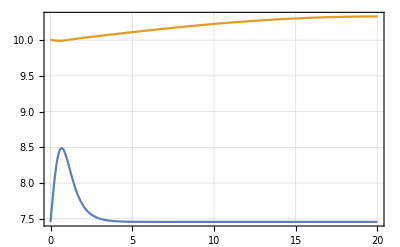

```mathematica
Show[Plot[Evaluate[funs+vals],{r,0,rmax},PlotRange->All],
Plot[V[V0,r],{r,0,rmax},PlotRange->All,PlotStyle->Black],PlotRange->All,Axes->False, Frame->True, FrameStyle->Large,GridLines->Automatic]
```

```mathematica
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
sp[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
cp[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

```mathematica
l1=0;
l2=0;
a=1.;
V11=-40.0;
V22=-50.0;
V12=1;
Ε=1.5;
rmin=0.0;
rmax=5;
Eth={0.0,40.0};
```

```mathematica
sol1=NDSolve[{
-u1''[r]-Ε u1[r]==-(V11 Exp[-r^2/a^2]+(l1(l1+1))/r^2+Eth[[1]])u1[r]-(V12) Exp[-r^2/a^2]u2[r],
-u2''[r]-Ε u2[r]==-(V12) Exp[-r^2/a^2]u1[r]-(V22 Exp[-r^2/a^2]+(l2(l2+1))/r^2+Eth[[2]])u2[r],
u1[rmin]==0,
u1'[rmin]==1,
u2[rmin]==0,
u2[rmax]==0
},
{u1[r],u2[r]},{r,rmin,rmax},
Method->"ExplicitRungeKutta"];
```

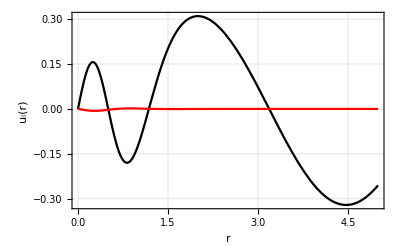

```mathematica
Plot[{u1[r]/.sol1,u2[r]/.sol1},{r,rmin,rmax},PlotRange->All,PlotStyle->{Black,Red},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"r","u_i(r)"}]
```

```mathematica
FindK[l1_,l2_,a_,V11_,V22_,V12_,Eth_,rmin_,rmax_,Ε_]:=Module[{K,r,u1,u2,Y,sol1,k},
sol1=NDSolve[{
-u1''[r]+(V11 Exp[-r^2/a^2]+(l1(l1+1))/r^2+Eth[[1]])u1[r]+V12 Exp[-r^2/a^2]u2[r]==Ε u1[r],
-u2''[r]+V12 Exp[-r^2/a^2]u1[r]+(V22 Exp[-r^2/a^2]+(l2(l2+1))/r^2+Eth[[2]])u2[r]==Ε u2[r],
u1[rmin]==0,
u1'[rmin]==1,
u2[rmin]==0,
If[Ε<Eth[[2]],u2[rmax]==0,u2'[rmin]==0]},
{u1[r],u2[r]},{r,rmin,rmax},
Method->"ExplicitRungeKutta"];
k=√(Ε-Eth[[1]]);
Y=D[Log[u1[r]/.sol1[[1]]],r]/.r->rmax;
K=-(sp[0,k,rmax]-Y se[0,k,rmax])/(cp[0,k,rmax] - Y ce[0,k,rmax]);
K
]
```

```mathematica
Kdat=Table[{EE,FindK[0,0,1,-1.0,-10.0,1.0,Eth,rmin,rmax,EE]},{EE,0.01,9.9,0.05}];
```

```mathematica
Kdat[[1]]
```

{0.01,0.0696699}

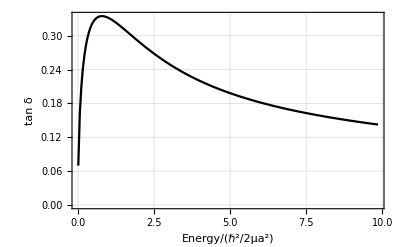

```mathematica
ListPlot[Kdat,Joined->True,Frame->True,LabelStyle->Large,PlotStyle->Black,GridLines->Automatic,FrameLabel->{"Energy/(ℏ^2/2μa^2)","tan δ"}]
```

### General N-channel code...

Ok so let’s see if we can now construct a more general N-channel code with Mathematica!  I’ll start by re-defining our functions just so we have everything here in one place.

Let’s try using the Morse potential as the template for the single-channel potentials.  The Morse potential is:

V(r)=D_e (1-ⅇ^(-(r-r_e)/a))^2-D_e

```mathematica
Vmorse[a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De
```

The eigenvalues are:

E_n=-(λ-n-1/2)^2 ℏ^2/(2μ a^2)     with n=0,1,..., (λ-1/2)

where

λ=(a √(2μ D_e))/ℏ

Let x=r/a and the eigenfunctions are

u_n(r)=N_n z^(λ-n-1/2)ⅇ^(-1/2 z)L_n^(2λ-2n-1)(z)  with z=2λ ⅇ^(-(x-x_e)) and N_n=√((n!(2λ-2n-1))/(Γ(2λ-n)))

and L_n^(α)(z) is the generalized Laguerre polynomial.

The single-channel SE reads

-ℏ^2/(2μ)(∂^2 u(r))/(∂r^2)+(D_e (1-ⅇ^(-(r-r_e)/a))-D_e+(ℏ^2 l(l+1))/(2μ r^2))u(r)=E u(r)

The zero-energy scattering wavefunction looks like:

```mathematica
Clear[a,re,De,l];
```

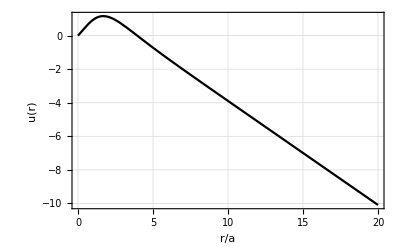

```mathematica
rmin=10^-6;rmax=20;sol=NDSolve[{-u''[r]+(Vmorse[a,re,De,r]+(l(l+1))/r^2-ksqr)u[r]==0/.{ksqr->0.00001,a->1,re->1,De->1,l->0},u[rmin]==0,u'[rmin]==1},u[r],{r,rmin,rmax}][[1]];
Plot[u[r]/.sol,{r,rmin,rmax},Frame->True,GridLines->Automatic,PlotStyle->Black,LabelStyle->Large,FrameLabel->{"r/a","u(r)"}]
```

What about the bound states?

```mathematica
μ=1/2;De=4;a=1;re=1;
l=0;rmin=0;rmax=20;{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+(Vmorse[a,re,De,r]+De+(l(l+1))/r^2)u[r],DirichletCondition[u[r]==0,r==rmin],DirichletCondition[u[r]==0,r==rmax]},u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
channel2states=vals-De
```

{-2.17469,-0.206454,0.0413376}

Compare to the (approximate?  got this from Wikipedia, so grain of salt here.) analytical values: E_n=-(λ-n-1/2)^2 ℏ^2/(2μ a^2)     with n=0,1,..., (λ-1/2), λ=(a √(2μ D_e))/ℏ

```mathematica
evals=Table[-(λ-n-0.5)^2/.λ->a √De/.μ->1/2,{n,0,2}]
```

{-2.25,-0.25,-0.25}

Deloff gives the analytical bound states Ε=-x^2/(2μ) at the zeros to

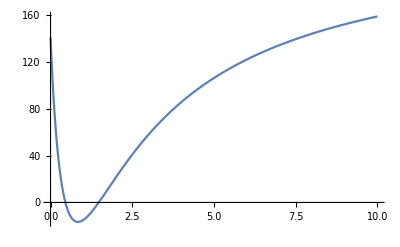

```mathematica
Plot[Hypergeometric1F1[1/2+x-√(2μ a^2 De),1+2x,2 ⅇ^(re/a)√(2μ a^2 De)],{x,0,10}]
```

```mathematica
evals[[2]]=-x^2/(2μ)/.FindRoot[Hypergeometric1F1[1/2+x-√(2μ a^2 De),1+2x,2 ⅇ^(re/a)√(2μ a^2 De)]==0,{x,.5}]
```

-0.206472

```mathematica
evals[[1]]=-x^2/(2μ)/.FindRoot[Hypergeometric1F1[1/2+x-√(2μ a^2 De),1+2x,2 ⅇ^(re/a)√(2μ a^2 De)]==0,{x,1.5}]
```

-2.17471

The relative errors are:

```mathematica
(evals-(channel2states))/evals
```

{9.72×10^-6,0.000088663,1.16535}

Which is not so bad, but I can’t seem to make it better by using a finer grid, which is troubling.

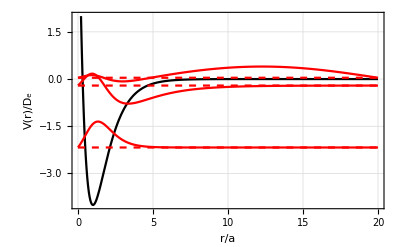

```mathematica
scalef=1.0;Plot[{Vmorse[a,re,De,r]+(l(l+1))/r^2,vals-De,scalef funs+vals-De},{r,0,rmax},PlotRange->{-De,2},Frame->True,GridLines->Automatic,PlotStyle->{{Black},{Red,Dashed},{Red}},LabelStyle->Large,FrameLabel->{"r/a","V(r)/D_e"}]
```

Before we can go any further, we must make some decisions about the model we want.  How many channels?  What is the energy range and how many channels are open?  What are the channel threshold values?  For this code I’ll keep the parameters of the potential fixed for the calculation and study the energy dependence of the potential.  Eventually we’ll want to make the thresholds magnetic field dependent and keep the energy fixed while changing the field.

```mathematica
Clear[k,se,ce,dse,dce,s,c,ds,dc,V12,V13,V21,V22,V33,V11,K,Ε,Eth,Nchan,Nopen,Nclosed]
```

```mathematica
Nchan=3;

Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
```

```mathematica
Clear[k,l,r]
```

```mathematica
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
dse[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
dce[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

I’ll also assume for simplicity that we only care about s-wave scattering.

```mathematica
Nopen[Emin_,Emax_,Eth_]:=Module[{nmin,nmax},
nmax=Length[Select[Eth,#<Emin &]];
nmin=Length[Select[Eth,#<Emax &]];
If[nmax≠nmin,0,nmin]
]
```

```mathematica
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
```

We must choose an energy range that lies between thresholds so the number of open channels is fixed through the calculation.  Let’s choose

```mathematica
Erange={Eth[[1]]+0.001,Eth[[2]]-0.001};
```

```mathematica
Nopen[Erange[[1]],Erange[[2]],Eth]
```

1

```mathematica
diagsc=Setupdiagsc[Ε,Nopen[Erange[[1]],Erange[[2]],Eth],Eth,r];
```

Access the diagonal s matrix by (and display as a matrix)

```mathematica
diagsc[[1]]//MatrixForm
```

((r (0.+Ε)^(1/4) SphericalBesselJ[0,r √(0.+Ε)])/(√π))

Now choose the form of the potential matrix:

```mathematica
Vdiag[r_,a_,re_,D11_,D22_,D33_,Eth_]:=({{Vmorse[a,re,D11,r]+Eth[[1]], 0, 0}, {0, Vmorse[a,re,D22,r]+Eth[[2]], 0}, {0, 0, Vmorse[a,re,D33,r]+Eth[[3]]}});
Vcoupling[r_,a_,V12_,V23_,r12_,r23_,a12_,a23_]:=({{0, V12 ⅇ^(-(r-r12)^2/a12^2), 0}, {V12 ⅇ^(-(r-r12)^2/a12^2), 0, V23 ⅇ^(-(r-r23)^2/a23^2)}, {0, V23 ⅇ^(-(r-r23)^2/a23^2), 0}});
```

```mathematica
Vmat[r_,a_,re_,D11_,D22_,D33_,V12_,V23_,r12_,r23_,a12_,a23_,Eth_]:=Vdiag[r,a,re,D11,D22,D33,Eth]+Vcoupling[r,a,V12,V23,r12,r23,a12,a23]
```

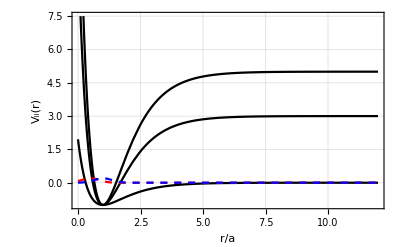

```mathematica
vcscale=1;Clear[VV];VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];Plot[{Diagonal[VV[r]],vcscale VV[r][[1,2]],vcscale VV[r][[2,3]]},{r,rmin,rmax},Frame->True,GridLines->Automatic,PlotStyle->{{Black},{Red,Dashed},{Blue,Dashed}},LabelStyle->Large,FrameLabel->{"r/a","V_ii(r)"}]
```

```mathematica
no=Nopen[Erange[[1]],Erange[[2]],Eth];
Clear[umat,u];
umat[r_]=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,Nchan}];
```

```mathematica
eqs[r_,Ε_]:=Table[-umat''[r][[i,α]]+Sum[(VV[r][[i,j]])umat[r][[j,α]],{j,1,Nchan}]-Ε umat[r][[i,α]]==0,{i,1,Nchan},{α,1,Nchan}];
```

```mathematica
boundarycond[Ε_]:=Table[{
umat[rmin][[i,α]]==0,
If[Ε<Eth[[i]],
umat[rmax][[i,α]]==0,
umat'[rmin][[i,α]]==KroneckerDelta[i,α]]},
{i,1,Nchan},{α,1,Nchan}];
```

```mathematica
alleqs[r_,Ε_]:=Table[Flatten[{Transpose[eqs[r,Ε]][[α]],Transpose[boundarycond[Ε]][[α]]}],{α,1,Nchan}]
```

```mathematica
Erange
```

{0.001,2.999}

```mathematica
Εtest=4.5; (*2 channels open*)
α=1;rmax=15;sol1=NDSolve[alleqs[r,Εtest][[α]],umat[r][[1;;Nchan,α]],{r,rmin,rmax},Method->{"Automatic"}];
```

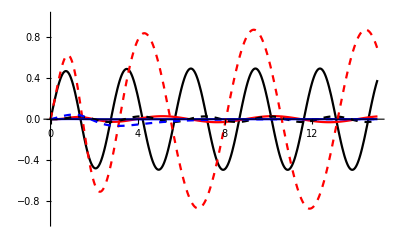

```mathematica
p1=Plot[Evaluate[Table[Subscript[u, i,α][r],{i,1,3}]/.sol1],{r,rmin,rmax},PlotStyle->{{Black},{Red},{Blue}},PlotRange->{-1,1}];
α=2;
sol2=NDSolve[alleqs[r,Εtest][[α]],umat[r][[1;;Nchan,α]],{r,rmin,rmax},Method->"Automatic"];
p2=Plot[Evaluate[Table[Subscript[u, i,α][r],{i,1,3}]/.sol2],{r,rmin,rmax},PlotStyle->{{Black,Dashed},{Red,Dashed},{Blue,Dashed}},PlotRange->{-1,1}];
Show[{p1,p2}]
```

```mathematica
umat[r]/.sol1/.sol2
```

{{{{InterpolatingFunction[{{0., 15.}}, <>][r],InterpolatingFunction[{{0., 15.}}, <>][r],u_(1,3)[r]},{InterpolatingFunction[{{0., 15.}}, <>][r],InterpolatingFunction[{{0., 15.}}, <>][r],u_(2,3)[r]},{InterpolatingFunction[{{0., 15.}}, <>][r],InterpolatingFunction[{{0., 15.}}, <>][r],u_(3,3)[r]}}}}

### Okay, let’s try to put it all together into a module that calculates the K matrix at one energy.

```mathematica
Nopen[Emin_,Emax_,Eth_]:=Module[{nmin,nmax},
nmax=Length[Select[Eth,#<Emin &]];
nmin=Length[Select[Eth,#<Emax &]];
If[nmax≠nmin,0,nmin]
]
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
SetupPotentialMorse3Channel[r_,Eth_,a_,re_,D11_,D22_,D33_,V12_,V23_,r12_,a12_,r23_,a23_]:=Module[{},
Vdiag=({{Vmorse[a,re,D11,r]+Eth[[1]], 0, 0}, {0, Vmorse[a,re,D22,r]+Eth[[2]], 0}, {0, 0, Vmorse[a,re,D33,r]+Eth[[3]]}});
Vcoupling=({{0, V12 ⅇ^(-(r-r12)^2/a12^2), 0}, {V12 ⅇ^(-(r-r12)^2/a12^2), 0, V23 ⅇ^(-(r-r23)^2/a23^2)}, {0, V23 ⅇ^(-(r-r23)^2/a23^2), 0}});
Return[Vdiag+Vcoupling]
]
```

```mathematica
Nchan=2;
Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
no=1;
Erange=Which[
no==1,{Eth[[1]]+0.001,Eth[[2]]-0.001},
no==2,{Eth[[2]]+0.001,Eth[[3]]-0.001},
no==3,{Eth[[3]]+0.001,Eth[[3]]+10.0}];
VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];
eqs[Ε_,r_,u_,Vmat_,Nchan_]:=Table[-Subscript[u, i,α]''[r]+Sum[VV[r][[i,j]]Subscript[u, j,α][r],{j,1,Nchan}]-Ε Subscript[u, i,α][r]==0,{i,1,Nchan},{α,1,Nchan}];
boundarycond[Ε_,rmin_,rmax_,Eth_,Nchan_,u_]:=Module[{},
Table[{
Subscript[u, ii,β][rmin]==0,
With[{i=ii,α=β},If[Ε<Eth[[i]],
Subscript[u, i,α][rmax]==0,
Subscript[u, i,α]'[rmin]==KroneckerDelta[i,α]]]},
{ii,1,Nchan},{β,1,Nchan}]
];
```

```mathematica
VV[x]//MatrixForm
```

(-1.+1. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-0.5+x)^2) | 0
0.2 ⅇ^(-4. (-0.5+x)^2) | -1.+4. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-1.+x)^2)
0 | 0.2 ⅇ^(-4. (-1.+x)^2) | -1.+6. (1-ⅇ^(1-x))^2)

```mathematica
alleqs[Ε_,r_,rmin_,rmax_,Eth_,Nchan_,u_,Vmat_]:=Table[Flatten[{Transpose[eqs[Ε,r,u,Vmat,Nchan]][[i]],Transpose[boundarycond[Ε,rmin,rmax,Eth,Nchan,u]][[i]]}],{i,1,Nchan}];
diagsc=Setupdiagsc[Ε,no,Eth,r];
```

```mathematica
diagsc[[2,1,1]]
```

-(r (0.+Ε)^(1/4) SphericalBesselY[0,r √(0.+Ε)])/(√π)

```mathematica
Etest=Erange[[1]]+0.01;
equations=alleqs[Etest,r,rmin,rmax,Eth,Nchan,u,VV[r]];
```

```mathematica
umat=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,1,Nchan}];
```

```mathematica
NDSolve[equations[[1]],umatᵀ[[1]],{r,rmin,rmax},Method->{"Automatic"}]
```

{{u_(1,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r],u_(2,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r]}}

```mathematica
sols=Flatten[Table[NDSolve[equations[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,Nchan}]];
k=Table[√(Etest-Eth[[i]]),{i,1,no}];
```

```mathematica
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
```

```mathematica
uopen[[1]]
```

{InterpolatingFunction[{{0., 12.}}, <>][r]}

```mathematica
Unprotect[Kmatrix];Kmatrix[Eth_,nchan_,no_,r_,rmin_,rmax_,Vmat_,Ε_]:=Module[{K,Y,Imat,Jmat,sols,eqs,uopen,umat,u,i,j,α,β,diagsc,S},
diagsc=Setupdiagsc[Ε,no,Eth,r];
umat=Table[Subscript[u, i,j][r],{i,1,nchan},{j,1,nchan}];
eqs=alleqs[Ε,r,rmin,rmax,Eth,nchan,u,Vmat];
(*Print[eqs[[1]]];*)
sols=Flatten[Table[NDSolve[eqs[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,nchan}]];
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
Imat=Table[Wronskian[{uopen[[i,β]],diagsc[[2,i,i]]},r]/Wronskian[{diagsc[[1,i,i]],diagsc[[2,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;Jmat=Table[Wronskian[{uopen[[i,β]],diagsc[[1,i,i]]},r]/Wronskian[{diagsc[[2,i,i]],diagsc[[1,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;
(*Y=(D[Log[uopen],r]/.r->rmax)/.r->rmax;*)
K=Jmat.Inverse[Imat]/.r->rmax;
(*K=-(diagsc[[3]]-Y.diagsc[[1]]).Inverse[diagsc[[4]]-Y.diagsc[[2]]];*)
S=(IdentityMatrix[no]+ⅈ K).Inverse[IdentityMatrix[no]-ⅈ K];
{K,S}
]
Protect[Kmatrix];
```

S=(1+ⅈ K)/(1-ⅈ K); f_(l=0)=√((4π)/(k_i k_j))(S_(i,j)-δ_(i,j))/(2ⅈ)

```mathematica
Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]
```

{{{0.683976,-0.0342022},{-0.0342021,-0.534191}},{{0.361496+0.931045 ⅈ,0.00542147-0.0494622 ⅈ},{0.00542145-0.0494621 ⅈ,0.55459-0.830634 ⅈ}}}

It’s hard to tell if this makes sense, so we’ll need to automate this process so we can look at the energy dependence and understand the results in terms of the single-channel solutions.

```mathematica
δ[De_,Ε_]:=Arg[Hypergeometric1F1[1/2+ⅈ √Ε-√(a^2 De),1+2ⅈ √Ε,2 ⅇ^(re/a)√(a^2 De)]]
```

```mathematica
dat=Table[{Etest,Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]},{Etest,Erange[[1]],Erange[[2]],0.002}];
```

```mathematica
dat[[1]]
```

{0.001,{{{-0.117912}},{{0.972575-0.23259 ⅈ}}}}

```mathematica
K11=Table[{dat[[n,1]],dat[[n,2,1,1,1]]},{n,1,Length[dat]}];
(*K12=Table[{dat[[n,1]],dat[[n,2,2]]},{n,1,Length[dat]}];
K21=Table[{dat[[n,1]],dat[[n,2,3]]},{n,1,Length[dat]}];
K22=Table[{dat[[n,1]],dat[[n,2,4]]},{n,1,Length[dat]}];*)
```

```mathematica
K11[[1]]
```

{0.001,-0.117912}

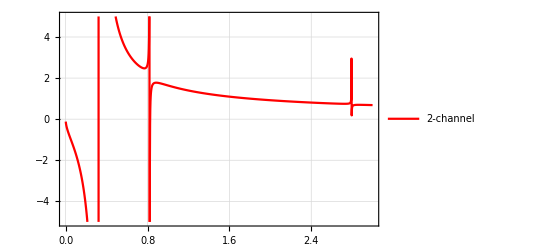

```mathematica
KK=ListPlot[Legended[K11,"2-channel"],Joined->True,Frame->True,PlotStyle->Red,GridLines->Automatic,PlotRange->{-5,5}]
```

```mathematica
De=4;a=1;re=1;
l=0;rmin=0;rmax=20;{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+(Vmorse[a,re,De,r]+De+(l(l+1))/r^2)u[r],DirichletCondition[u[r]==0,r==rmin],DirichletCondition[u[r]==0,r==rmax]},u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
channel2states=vals-De+Eth[[2]]
```

{0.825315,2.79355,3.04134}

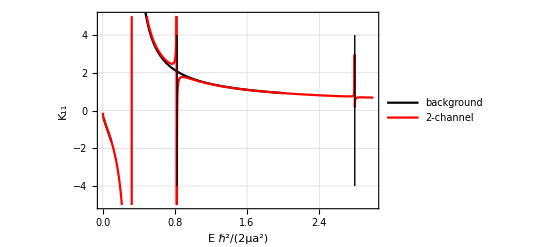

```mathematica
Show[Plot[Legended[Tan[δ[1,Ε]],"background"],{Ε,0.01,2.0},PlotStyle->Black],KK,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_11"} ,Epilog->{Style[Line[{{0.825315,-4},{0.825315,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

The dashed vertical lines indicate the numerically found positions of the bound states in the excited channel.  Looks like good agreement!

Let’s look at (k_i k_j)/(4π)(|f|)^2=(k_i k_j)/(4π)(|(S_ij-δ_ij)/(2ⅈ)|)^2

### scratch work for the single-channel Morse potential

The single-channel result is known analytically.  See Deloff, Ann. Phys. (2007).  Deloff parameterizes the potential as V=-s/(2μ a^2)ⅇ^(-(r-d)/a)(2-ⅇ^(-(r-d)/a))

V=-s/(2μ a^2)ⅇ^(-(r-d)/a)(2-ⅇ^(-(r-d)/a))

which can be written:

V=s/(2μ a^2)(ⅇ^(-2(r-d)/a)-2 ⅇ^(-(r-d)/a))

which is equivalent to our V_morse with D_e=s/(2μ a^2) and d=r_e.

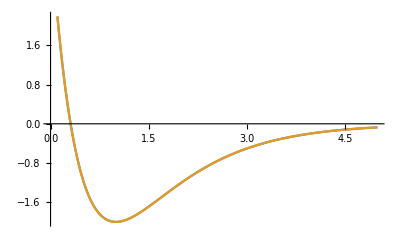

```mathematica
Plot[{-s/a^2 ⅇ^((d-r)/a)(2-ⅇ^((d-r)/a))/.{d->1,s->2},Vmorse[a,re,s/a^2,r]/.s->2},{r,0,5}]
```

The phase shift is

```mathematica
δ[s_,ξ_,z_]:=Arg[Hypergeometric1F1[1/2+ⅈ ξ-√s,1+2ⅈ ξ,z]]
```

where ξ is the center of mass momentum √(2μ Ε) and z=2 ⅇ^(d/a)√(|s|), with s=2μ a^2 D_e

```mathematica
δ[De_,Ε_]:=Arg[Hypergeometric1F1[1/2+ⅈ √Ε-√(a^2 De),1+2ⅈ √Ε,2 ⅇ^(re/a)√(a^2 De)]]
```

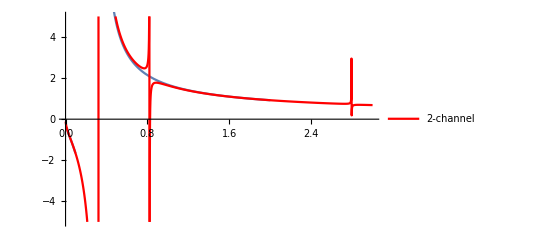

```mathematica
Show[Plot[Tan[δ[1,Ε]],{Ε,0.01,2.0}],KK,PlotRange->{-5,5}]
```

Okay!  That looks right.  So it looks like there is a minus sign issue with K but otherwise the single-channel result agrees with the analytical expression given by Deloff.

### 3-channel calculation

```mathematica
Nchan=3;
Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
no=1;
Erange=Which[
no==1,{Eth[[1]]+0.001,Eth[[2]]-0.001},
no==2,{Eth[[2]]+0.001,Eth[[3]]-0.001},
no==3,{Eth[[3]]+0.001,Eth[[3]]+10.0}];
VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];
```

```mathematica
VV[x]//MatrixForm
```

(-1.+1. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-0.5+x)^2) | 0
0.2 ⅇ^(-4. (-0.5+x)^2) | -1.+4. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-1.+x)^2)
0 | 0.2 ⅇ^(-4. (-1.+x)^2) | -1.+6. (1-ⅇ^(1-x))^2)

```mathematica
diagsc=Setupdiagsc[Ε,no,Eth,r];
```

```mathematica
Etest=Erange[[1]]+0.01;
equations=alleqs[Etest,r,rmin,rmax,Eth,Nchan,u,VV[r]];
```

```mathematica
umat=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,1,Nchan}];
```

```mathematica
NDSolve[equations[[1]],umatᵀ[[1]],{r,rmin,rmax},Method->{"Automatic"}]
```

{{u_(1,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r],u_(2,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r],u_(3,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r]}}

```mathematica
sols=Flatten[Table[NDSolve[equations[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,Nchan}]];
k=Table[√(Etest-Eth[[i]]),{i,1,no}];
```

```mathematica
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
```

```mathematica
uopen[[1]]
```

{InterpolatingFunction[{{0., 12.}}, <>][r]}

```mathematica
Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]
```

{{{-0.403548}},{{0.719911-0.694067 ⅈ}}}

```mathematica
δ[De_,Ε_]:=Arg[Hypergeometric1F1[1/2+ⅈ √Ε-√(a^2 De),1+2ⅈ √Ε,2 ⅇ^(re/a)√(a^2 De)]]
```

```mathematica
dat=Table[{Etest,Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]},{Etest,Erange[[1]],Erange[[2]],0.002}];
```

NDSolve::ndsz: At r == 3.85186×10^-34, step size is effectively zero; singularity or stiff system suspected.

```mathematica
dat[[1]]
```

{0.001,{{{-0.117909}},{{0.972576-0.232584 ⅈ}}}}

```mathematica
K11=Table[{dat[[n,1]],dat[[n,2,1,1,1]]},{n,1,Length[dat]}];
(*K12=Table[{dat[[n,1]],dat[[n,2,2]]},{n,1,Length[dat]}];
K21=Table[{dat[[n,1]],dat[[n,2,3]]},{n,1,Length[dat]}];
K22=Table[{dat[[n,1]],dat[[n,2,4]]},{n,1,Length[dat]}];*)
```

```mathematica
K11[[1]]
```

{0.001,-0.117909}

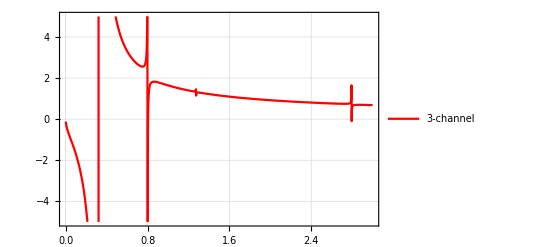

```mathematica
KK=ListPlot[Legended[K11,"3-channel"],Joined->True,Frame->True,PlotStyle->Red,GridLines->Automatic,PlotRange->{-5,5}]
```

```mathematica
De=6;a=1;re=1;
l=0;rmin=0;rmax=20;{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+(Vmorse[a,re,De,r]+De+(l(l+1))/r^2)u[r],DirichletCondition[u[r]==0,r==rmin],DirichletCondition[u[r]==0,r==rmax]},u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
channel3states=vals-De+Eth[[3]]
```

{1.25722,4.15818,5.01988}

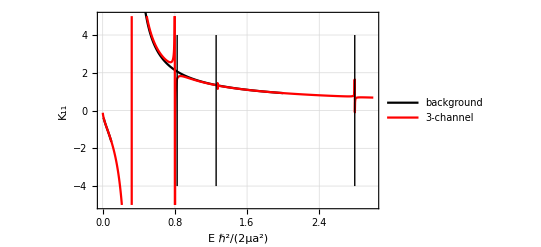

```mathematica
Show[Plot[Legended[Tan[δ[1,Ε]],"background"],{Ε,0.01,2.0},PlotStyle->Black],KK,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_11"} ,Epilog->{Style[Line[{{0.825315,-4},{0.825315,4}}],Dashed],Style[Line[{{1.257222782,-4},{1.257222782,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

### 2 open channels

```mathematica
Nchan=3;
Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
no=2;
Erange=Which[
no==1,{Eth[[1]]+0.001,Eth[[2]]-0.001},
no==2,{Eth[[2]]+0.001,Eth[[3]]-0.001},
no==3,{Eth[[3]]+0.001,Eth[[3]]+10.0}];
VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];
```

```mathematica
VV[x]//MatrixForm
```

(-1.+1. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-0.5+x)^2) | 0
0.2 ⅇ^(-4. (-0.5+x)^2) | -1.+4. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-1.+x)^2)
0 | 0.2 ⅇ^(-4. (-1.+x)^2) | -1.+6. (1-ⅇ^(1-x))^2)

```mathematica
diagsc=Setupdiagsc[Ε,no,Eth,r];
```

```mathematica
Etest=Erange[[1]]+0.01;
equations=alleqs[Etest,r,rmin,rmax,Eth,Nchan,u,VV[r]];
```

```mathematica
umat=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,1,Nchan}];
```

```mathematica
NDSolve[equations[[1]],umatᵀ[[1]],{r,rmin,rmax},Method->{"Automatic"}]
```

{{u_(1,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r],u_(2,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r],u_(3,1)[r]→InterpolatingFunction[{{0., 12.}}, <>][r]}}

```mathematica
sols=Flatten[Table[NDSolve[equations[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,Nchan}]];
```

```mathematica
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
```

```mathematica
uopen
```

{{InterpolatingFunction[{{0., 12.}}, <>][r],InterpolatingFunction[{{0., 12.}}, <>][r]},{InterpolatingFunction[{{0., 12.}}, <>][r],InterpolatingFunction[{{0., 12.}}, <>][r]}}

```mathematica
diagsc[[1]]//MatrixForm
```

((r (0.+Ε)^(1/4) SphericalBesselJ[0,r √(0.+Ε)])/(√π) | 0.
0. | (r (-3.+Ε)^(1/4) SphericalBesselJ[0,r √(-3.+Ε)])/(√π))

```mathematica
Imat=Table[Wronskian[{uopen[[i,β]],diagsc[[2,i,i]]},r]/Wronskian[{diagsc[[1,i,i]],diagsc[[2,i,i]]},r],{i,1,no},{β,1,no}]/.{Ε->Etest};
```

```mathematica
Jmat=Table[Wronskian[{uopen[[i,β]],diagsc[[1,i,i]]},r]/Wronskian[{diagsc[[1,i,i]],diagsc[[2,i,i]]},r],{i,1,no},{β,1,no}]/.{Ε->Etest};
```

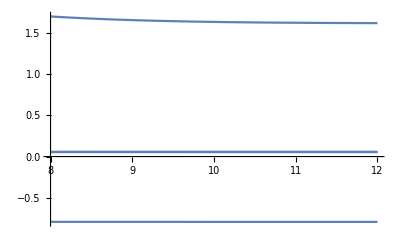

```mathematica
Plot[Flatten[Jmat],{r,8.0,12.0}]
```

```mathematica
K=Jmat.Inverse[Imat]/.{Ε->Etest,r->10.}//MatrixForm
```

(-0.683905 | 0.0341217
0.0341216 | 0.537825)

```mathematica
K=Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]
```

{{{0.683976,-0.0342022},{-0.0342021,-0.534191}},{{0.361496+0.931045 ⅈ,0.00542147-0.0494622 ⅈ},{0.00542145-0.0494621 ⅈ,0.55459-0.830634 ⅈ}}}

```mathematica
MatrixForm[K[[1]]]
```

(0.683976 | -0.0342022
-0.0342021 | -0.534191)

Yay!  This is symmetric!

```mathematica
SS=K[[2]];MatrixForm[SS]
```

(0.361496+0.931045 ⅈ | 0.00542147-0.0494622 ⅈ
0.00542145-0.0494621 ⅈ | 0.55459-0.830634 ⅈ)

```mathematica
MatrixForm[SSᵀ*.SS]
```

(1.+0. ⅈ | -1.65098×10^-7-8.58522×10^-8 ⅈ
-1.65098×10^-7+8.58522×10^-8 ⅈ | 1.+0. ⅈ)

Yay!  It looks unitary to expected accuracy.

```mathematica
dat=Table[{Etest,Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]},{Etest,Erange[[1]],Erange[[2]],0.002}];
```

```mathematica
dat[[1]]
```

{3.001,{{{0.685983,-0.0170517},{-0.0170517,-0.150541}},{{0.35982+0.932607 ⅈ,0.0121369-0.0250144 ⅈ},{0.0121368-0.0250143 ⅈ,0.955232-0.294549 ⅈ}}}}

```mathematica
K11=Table[{dat[[n,1]],dat[[n,2,1,1,1]]},{n,1,Length[dat]}];
K12=Table[{dat[[n,1]],dat[[n,2,1,1,2]]},{n,1,Length[dat]}];
K21=Table[{dat[[n,1]],dat[[n,2,1,2,1]]},{n,1,Length[dat]}];
K22=Table[{dat[[n,1]],dat[[n,2,1,2,2]]},{n,1,Length[dat]}];
```

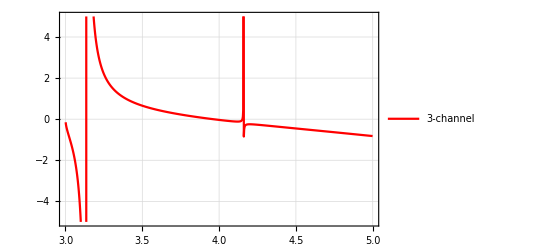

```mathematica
KK=ListPlot[Legended[K22,"3-channel"],Joined->True,Frame->True,PlotStyle->Red,GridLines->Automatic,PlotRange->{-5,5}]
```

```mathematica
De=6;a=1;re=1;
l=0;rmin=0;rmax=20;{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+(Vmorse[a,re,De,r]+De+(l(l+1))/r^2)u[r],DirichletCondition[u[r]==0,r==rmin],DirichletCondition[u[r]==0,r==rmax]},u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
channel3states=vals-De+Eth[[3]]
```

{1.25722,4.15818,5.01988}

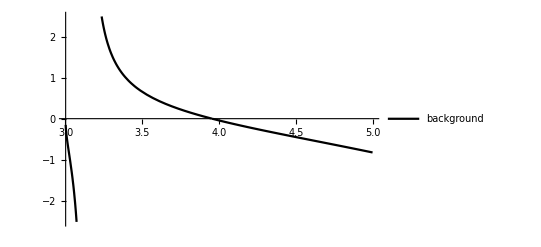

```mathematica
Plot[Legended[Tan[δ[4,Ε-Eth[[2]]]],"background"],{Ε,Erange[[1]],Erange[[2]]},PlotStyle->{Thick,Black}]
```

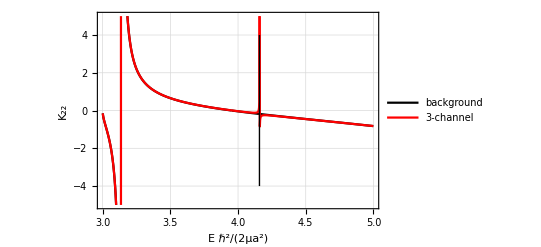

```mathematica
Show[Plot[Legended[Tan[δ[4,Ε-Eth[[2]]]],"background"],{Ε,Erange[[1]],Erange[[2]]},PlotRange->{-5,5},PlotStyle->{Thick,Black}],KK,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_22"} ,Epilog->{Style[Line[{{4.1581812663427975,-4},{4.1581812663427975,4}}],Dashed],Style[Line[{{1.257222782,-4},{1.257222782,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

Okay so it looks like there is one resonance feature here that coincides with the position of a bound state attached to the 3rd channel.  That position is indicated by the vertical dashed line.

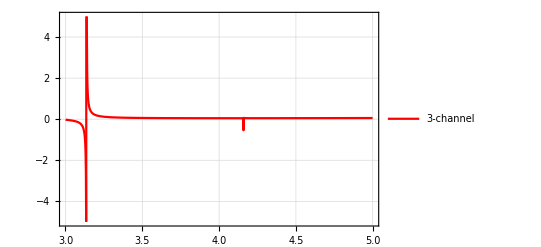

```mathematica
KK21=ListPlot[Legended[K21,"3-channel"],Joined->True,Frame->True,PlotStyle->Red,GridLines->Automatic,PlotRange->{-5,5}]
```

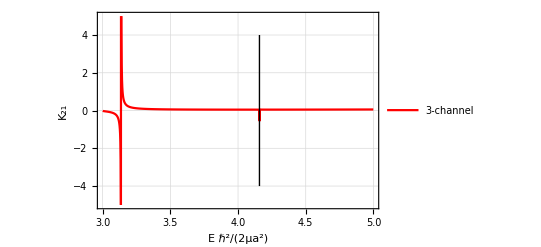

```mathematica
Show[KK21,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_21"} ,Epilog->{Style[Line[{{4.1581812663427975,-4},{4.1581812663427975,4}}],Dashed],Style[Line[{{1.257222782,-4},{1.257222782,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

```mathematica
SS=dat[[1,2,2]]
```

{{0.35982+0.932607 ⅈ,0.0121369-0.0250144 ⅈ},{0.0121368-0.0250143 ⅈ,0.955232-0.294549 ⅈ}}

```mathematica
SS//MatrixForm
```

(0.35982+0.932607 ⅈ | 0.0121369-0.0250144 ⅈ
0.0121368-0.0250143 ⅈ | 0.955232-0.294549 ⅈ)

```mathematica
MatrixForm[SSᵀ*]
```

(0.35982-0.932607 ⅈ | 0.0121368+0.0250143 ⅈ
0.0121369+0.0250144 ⅈ | 0.955232+0.294549 ⅈ)

```mathematica
Simplify[SSᵀ*.SS]//MatrixForm
```

(1.+0. ⅈ | -7.71722×10^-8-8.26997×10^-8 ⅈ
-7.71722×10^-8+8.26997×10^-8 ⅈ | 1.+0. ⅈ)